```mathematica
Integrate[L^(3n+2)Exp[(2n-k)q E0 L/2/kB/T],{L,0,Lc}]
```

ConditionalExpression[(8^(1+n) kB^3 Lc^(3 n) ((E0 Lc (k-2 n) q)/(kB T))^(-3 n) T^3 (Gamma[3+3 n]-Gamma[3 (1+n),(E0 Lc (k-2 n) q)/(2 kB T)]))/(E0^3 (k-2 n)^3 q^3),Re[n]>-1]

```mathematica
FullSimplify[(8^(1+n) kB^3 Lc^(3 n) ((E0 Lc (k-2 n) q)/(kB T))^(-3 n) T^3 (Gamma[3+3 n]-Gamma[3 (1+n),(E0 Lc (k-2 n) q)/(2 kB T)]))/(E0^3 (k-2 n)^3 q^3),Assumptions->kB>0&&T>0&&Lc>0&&E0>0&&q>0&&0≤k≤ n/2&&n>0&&n ∈Integers]
```

(-1)^n 8^(1+n) (-(E0 (k-2 n) q)/(kB T))^(-3 (1+n)) (-Gamma[3+3 n]+Gamma[3 (1+n),(E0 Lc (k-2 n) q)/(2 kB T)])

```mathematica
Gamma[9,-10]
```

54133120 ⅇ^10

```mathematica
Integrate[P L^(3n+2)/kB/T Exp[-P L^3/kB/T-(n+k)q E0 L/kB/T],{L,0,Infinity}]//Together//FullSimplify
```

ConditionalExpression[1/(6 kB^2 T^2)(P/(kB T))^(-1-n) (2 kB P T Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)])),Re[n]>-1&&Re[P/(kB T)]>0&&Re[(E0 (k+n) q)/(kB T)]>0]

```mathematica
Coefficient[1/(6 kB^2 T^2)(P/(kB T))^(-1-n) (2 kB P T Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]]//FullSimplify
```

-(E0 (k+n) q (P/(kB T))^(2/3-n) Gamma[4/3+n])/(3 P)

```mathematica
Coefficient[1/(6 kB^2 T^2)(P/(kB T))^(-1-n) (2 kB P T Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]]//FullSimplify
```

(E0^2 (k+n)^2 q^2 (P/(kB T))^(-2/3-n) Gamma[5/3+n])/(6 kB^2 T^2)

```mathematica
Coefficient[1/(6 kB^2 T^2)(P/(kB T))^(-1-n) (2 kB P T Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]+E0 (k+n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)])), HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k+n)^3 q^3)/(27 kB^2 P T^2)]]//FullSimplify
```

1/3 (P/(kB T))^-n Gamma[1+n]

```mathematica
Integrate[P L^(3n+2)/kB/T Exp[-P L^3/kB/T+(2n-k)q E0 L/2/kB/T],{L,0,Infinity}]
```

ConditionalExpression[1/(24 kB P T)(P/(kB T))^-n (8 kB P T Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q (P/(kB T))^(1/3) (-4 kB (P/(kB T))^(1/3) T Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)])),Re[n]>-1&&Re[P/(kB T)]>0&&Re[(E0 (k-2 n) q)/(kB T)]>0]

```mathematica
Integrate[P L^(3n+2)/kB/T Exp[-P L^3/kB/T+(2n-k)q E0 L/2/kB/T],{L,0,Infinity},Assumptions->0<k<n/2]
```

ConditionalExpression[1/(24 kB P T)(P/(kB T))^-n (8 kB P T Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q (P/(kB T))^(1/3) (-4 kB (P/(kB T))^(1/3) T Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)])),Re[(E0 q)/(kB T)]<0&&Re[P/(kB T)]>0]

```mathematica
Integrate[P L^(3n+2)/kB/T Exp[-P L^3/kB/T+(2n-k)q E0 L/2/kB/T],{L,0,Infinity},Assumptions->0<k<n/2&& q E0>0&&kB>0&&T>0&&P>0]
```

1/24 P^(-2/3-n) (kB T)^(-4/3+n) (8 P^(2/3) (kB T)^(4/3) Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q (-4 P^(1/3) (kB T)^(2/3) Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]))

```mathematica
Coefficient[1/24 P^(-2/3-n) (kB T)^(-4/3+n) (8 P^(2/3) (kB T)^(4/3) Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q (-4 P^(1/3) (kB T)^(2/3) Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)])),HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

1/3 P^-n (kB T)^n Gamma[1+n]

```mathematica
Coefficient[1/24 P^(-2/3-n) (kB T)^(-4/3+n) (8 P^(2/3) (kB T)^(4/3) Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q (-4 P^(1/3) (kB T)^(2/3) Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)])),HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

-1/6 E0 (k-2 n) P^(-1/3-n) q (kB T)^(-2/3+n) Gamma[4/3+n]

```mathematica
Coefficient[1/24 P^(-2/3-n) (kB T)^(-4/3+n) (8 P^(2/3) (kB T)^(4/3) Gamma[1+n] HypergeometricPFQ[{1+n},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q (-4 P^(1/3) (kB T)^(2/3) Gamma[4/3+n] HypergeometricPFQ[{4/3+n},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 (k-2 n) q Gamma[5/3+n] HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)])),HypergeometricPFQ[{5/3+n},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

1/24 E0^2 (k-2 n)^2 P^(-2/3-n) q^2 (kB T)^(-4/3+n) Gamma[5/3+n]

```mathematica
Integrate[Exp[-p^2/2/m/kB/T],{p,-Infinity,Infinity}]
```

ConditionalExpression[(√(2 π))/(√(1/(kB m T))),Re[1/(kB m T)]>0]

```mathematica
Integrate[Exp[-q E0 x/kB/T],{x,L/2,L}]
```

(ⅇ^(-(E0 L q)/(kB T)) (-1+ⅇ^((E0 L q)/(2 kB T))) kB T)/(E0 q)

```mathematica
Integrate[P L^(n+2)/kB/T Exp[-P L^3/kB/T]Cosh[n q E0 L/kB/T](1-Exp[-q E0 L/2/kB/T])^(n/2),{L,0,Infinity}]
```

∫_0^∞ (ⅇ^(-(L^3 P)/(kB T)) (1-ⅇ^(-(E0 L q)/(2 kB T)))^(n/2) L^(2+n) P Cosh[(E0 L n q)/(kB T)])/(kB T)ⅆL

```mathematica
Table[Binomial[9,k],{k,0,9}]
```

{1,9,36,84,126,126,84,36,9,1}

```mathematica
Table[Binomial[9,k],{k,0,9}]//Length
```

10

```mathematica
Integrate[P L^(n+2)/kB/T Cosh[n q E0 L/kB/T]Exp[-P L^3/kB/T-k q E0 L/2/kB/T],{L,0,Infinity}]
```

ConditionalExpression[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))),Re[n]>-3&&Re[P/(kB T)]>0]

```mathematica
Coefficient[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))),HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

(E0^2 (k-2 n)^2 q^2 (P/(kB T))^(-2/3-n/3) Gamma[(5+n)/3])/(48 kB^2 T^2)

```mathematica
Coefficient[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))),HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

(E0^2 (k+2 n)^2 q^2 (P/(kB T))^(-2/3-n/3) Gamma[(5+n)/3])/(48 kB^2 T^2)

```mathematica
Coefficient[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))), HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

-(E0 (k-2 n) q (P/(kB T))^(2/3-n/3) Gamma[(4+n)/3])/(12 P)

```mathematica
Coefficient[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))), HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

-(E0 (k+2 n) q (P/(kB T))^(2/3-n/3) Gamma[(4+n)/3])/(12 P)

```mathematica
Coefficient[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))), HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

1/6 (P/(kB T))^(-n/3) Gamma[1+n/3]

```mathematica
Coefficient[1/(48 kB P T)(P/(kB T))^(-n/3) (8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+8 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q (P/(kB T))^(1/3) (-4 kB (k-2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]-4 kB (k+2 n) (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]+E0 q Gamma[(5+n)/3] ((k-2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k-2 n)^3 q^3)/(216 kB^2 P T^2)]+(k+2 n)^2 HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]))), HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 (k+2 n)^3 q^3)/(216 kB^2 P T^2)]]//FullSimplify
```

1/6 (P/(kB T))^(-n/3) Gamma[1+n/3]

```mathematica
Integrate[Exp[-q E0 x/kB/T],{x,0,L}]
```

((1-ⅇ^(-(E0 L q)/(kB T))) kB T)/(E0 q)

```mathematica
Integrate[Exp[q E0 x/kB/T],{x,0,L}]
```

((-1+ⅇ^((E0 L q)/(kB T))) kB T)/(E0 q)

```mathematica
Integrate[P L^(n+2)/kB/T Exp[-P L^3/kB/T-k q E0 L/kB/T],{L,0,Infinity}]
```

ConditionalExpression[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),Re[n]>-3&&Re[P/(kB T)]>0&&Re[(E0 k q)/(kB T)]>0]

```mathematica
Coefficient[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]]//FullSimplify
```

1/3 (P/(kB T))^(-n/3) Gamma[1+n/3]

```mathematica
Coefficient[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]]//FullSimplify
```

-(E0 k q (P/(kB T))^(2/3-n/3) Gamma[(4+n)/3])/(3 P)

```mathematica
Coefficient[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (-2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{5/3+n/3},{4/3,5/3},-(E0^3 k^3 q^3)/(27 kB^2 P T^2)]]//FullSimplify
```

(E0^2 k^2 q^2 (P/(kB T))^(-2/3-n/3) Gamma[(5+n)/3])/(6 kB^2 T^2)

```mathematica
Integrate[P L^(n+2)/kB/T Exp[-P L^3/kB/T+k q E0 L/kB/T],{L,0,Infinity}]
```

ConditionalExpression[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),Re[(E0 k q)/(kB T)]<0&&Re[n]>-3&&Re[P/(kB T)]>0]

```mathematica
FullSimplify[Coefficient[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{1+n/3},{1/3,2/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]]]
```

1/3 (P/(kB T))^(-n/3) Gamma[1+n/3]

```mathematica
FullSimplify[Coefficient[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{4/3+n/3},{2/3,4/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]]]
```

(E0 k q (P/(kB T))^(2/3-n/3) Gamma[(4+n)/3])/(3 P)

```mathematica
FullSimplify[Coefficient[1/(6 kB P T)(P/(kB T))^(-n/3) (2 kB P T Gamma[1+n/3] HypergeometricPFQ[{1+n/3},{1/3,2/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q (P/(kB T))^(1/3) (2 kB (P/(kB T))^(1/3) T Gamma[(4+n)/3] HypergeometricPFQ[{4/3+n/3},{2/3,4/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]+E0 k q Gamma[(5+n)/3] HypergeometricPFQ[{5/3+n/3},{4/3,5/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)])),HypergeometricPFQ[{5/3+n/3},{4/3,5/3},(E0^3 k^3 q^3)/(27 kB^2 P T^2)]]]
```

(E0^2 k^2 q^2 (P/(kB T))^(-2/3-n/3) Gamma[(5+n)/3])/(6 kB^2 T^2)

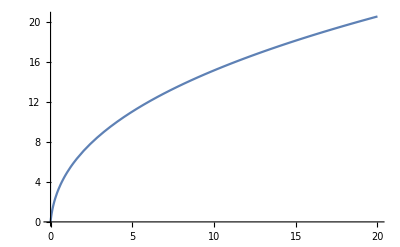

```mathematica
Plot[Log[HypergeometricPFQ[{5/3+100/3},{4/3,5/3},x]],{x,0,20}]
```